```mathematica
(*Tarea cuatro; Daniel Farid Calvo Ramos*)
a = 1; b = 20;
datos = Table[{x,N[x Sin[x]]},{x,a,b,1}]
```

{{1,0.841471},{2,1.81859},{3,0.42336},{4,-3.02721},{5,-4.79462},{6,-1.67649},{7,4.59891},{8,7.91487},{9,3.70907},{10,-5.44021},{11,-10.9999},{12,-6.43888},{13,5.46217},{14,13.8685},{15,9.75432},{16,-4.60645},{17,-16.3438},{18,-13.5178},{19,2.84767},{20,18.2589}}

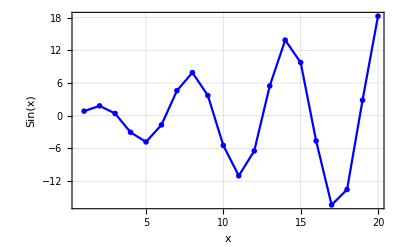

```mathematica
ListLinePlot[datos,
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["Sin(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}
]
```

```mathematica
LagrangeBaseElements[xs_,i_]:=Table[If[i≠ j,(x-xs[[j+1]])/(xs[[i+1]]-xs[[j+1]]),1],{j,0,Length[xs]-1}];
LagrangeBase[xs_,i_]:=Apply[Times,LagrangeBaseElements[xs,i]];
LagrangeBase[datos[[All,1]],0]
```

((2-x) (3-x) (4-x) (5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x))/121645100408832000

```mathematica
Total@Table[LagrangeBase[datos[[All,1]],i],{i,0,4}]
```

((2-x) (3-x) (4-x) (5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x))/121645100408832000+((3-x) (4-x) (5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-1+x))/6402373705728000+((4-x) (5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-2+x) (-1+x))/711374856192000+((5-x) (6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-3+x) (-2+x) (-1+x))/125536739328000+((6-x) (7-x) (8-x) (9-x) (10-x) (11-x) (12-x) (13-x) (14-x) (15-x) (16-x) (17-x) (18-x) (19-x) (20-x) (-4+x) (-3+x) (-2+x) (-1+x))/31384184832000

```mathematica
Expand@Total@Table[LagrangeBase[datos[[All,1]],i],{i,0,4}]
```

11629-(3076242287059 x)/77597520+(106251312544739 x^2)/1816214400-(305619972365189 x^3)/6054048000+(1511090098462513 x^4)/52306974720-(128045451605107 x^5)/10897286400+(16696288761680533 x^6)/4707627724800-(2137708358232001 x^7)/2615348736000+(28314510249031 x^8)/193133445120-(833755477693 x^9)/40236134400+(102037948363 x^10)/43893964800-(167005415747 x^11)/804722688000+(4263118931 x^12)/289700167680-(143514983 x^13)/174356582400+(14063429 x^14)/392302310400-(6222899 x^15)/5230697472000+(72931 x^16)/2510734786560-(1093 x^17)/2223046425600+(97 x^18)/18830510899200-x^19/39753300787200

```mathematica
LagrangeInterpolate[data_]:=Expand[data[[All,2]].Table[LagrangeBase[data[[All,1]],i],{i,0,Length[data]-1}]];
```

```mathematica
LagrangeInterpolate[datos]
```

-4.28042+15.6346 x-24.1109 x^2+23.9055 x^3-15.4381 x^4+7.0055 x^5-2.39772 x^6+0.635729 x^7-0.131739 x^8+0.0215491 x^9-0.00280737 x^10+0.000291782 x^11-0.0000240227 x^12+1.54529×10^-6 x^13-7.62178×10^-8 x^14+2.81128×10^-9 x^15-7.47874×10^-11 x^16+1.35277×10^-12 x^17-1.48782×10^-14 x^18+7.50715×10^-17 x^19

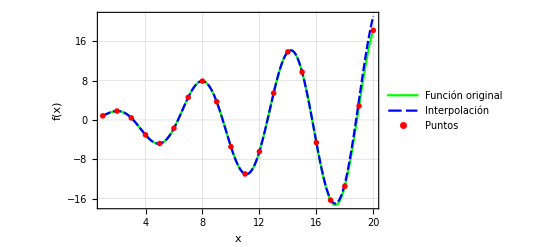

```mathematica
Show[
Plot[
{x Sin[x],-4.280419095302932+15.634601562283933 x-24.110855961218476 x^2+23.90548458416015 x^3-15.43812488252297 x^4+7.005500232568011 x^5-2.397716413717717 x^6+0.6357288305734983 x^7-0.1317387831004453 x^8+0.021549053608850954 x^9-0.0028073707411522264 x^10+0.0002917815917733435 x^11-0.000024022657475031295 x^12+1.5452864240289577*^-6 x^13-7.621784154678013*^-8 x^14+2.8112820605783687*^-9 x^15-7.478741939430898*^-11 x^16+1.3527733331341367*^-12 x^17-1.4878161156619692*^-14 x^18+7.507148066932835*^-17 x^19},
{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Green,Blue},PlotLegends->{"Función original","Interpolación"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

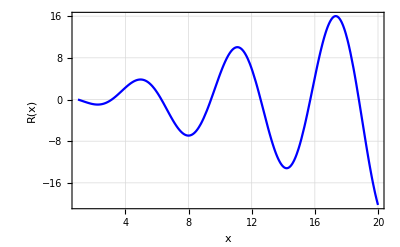

```mathematica
(*Analísis del error*)
R[x_]:=Sin[x]-(-4.280419095302932+15.634601562283933 x-24.110855961218476 x^2+23.90548458416015 x^3-15.43812488252297 x^4+7.005500232568011 x^5-2.397716413717717 x^6+0.6357288305734983 x^7-0.1317387831004453 x^8+0.021549053608850954 x^9-0.0028073707411522264 x^10+0.0002917815917733435 x^11-0.000024022657475031295 x^12+1.5452864240289577*^-6 x^13-7.621784154678013*^-8 x^14+2.8112820605783687*^-9 x^15-7.478741939430898*^-11 x^16+1.3527733331341367*^-12 x^17-1.4878161156619692*^-14 x^18+7.507148066932835*^-17 x^19);
Plot[R[x],{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["R(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}]
```

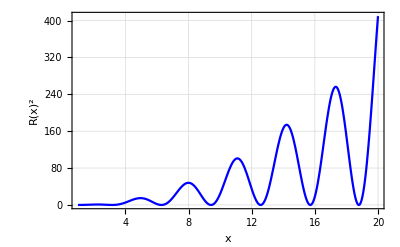

```mathematica
Plot[R[x]^2,{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["R(x)^2",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}]
```

```mathematica
ϵ = √NIntegrate[R[x]^2,{x,a,b}]
```

33.3052